```mathematica
Quit[];
```

```mathematica
u[t_,x_]:=(1/2)*(1+Tanh[(√2*x)/4-t/4]);
```

```mathematica
u[t,x]
```

1/2 (1-Tanh[t/4-x/(2 √2)])

```mathematica
u1=D[u[t,x],t]
```

-1/8 Sech[t/4-x/(2 √2)]^2

```mathematica
u2=D[u[t,x],x]
```

Sech[t/4-x/(2 √2)]^2/(4 √2)

```mathematica
u3=D[D[u[t,x],x],x]
```

1/8 Sech[t/4-x/(2 √2)]^2 Tanh[t/4-x/(2 √2)]

```mathematica
u1-u3-u[t,x]*(1-u[t,x])*(u[t,x]-1)
```

-1/8 Sech[t/4-x/(2 √2)]^2-1/2 (-1+1/2 (1-Tanh[t/4-x/(2 √2)])) (1+1/2 (-1+Tanh[t/4-x/(2 √2)])) (1-Tanh[t/4-x/(2 √2)])-1/8 Sech[t/4-x/(2 √2)]^2 Tanh[t/4-x/(2 √2)]

```mathematica
Simplify[u1-u3-u[t,x]*(1-u[t,x])*(u[t,x]-1)]
```

0

```mathematica
Quit[];
```

```mathematica
(*ξ=x-ct ->ODE c=√2/2 *)
```

```mathematica
u[ξ_]:=(1/2)*(1+Tanh[(√2*ξ)/4]);
```

```mathematica
u[ξ]
```

1/2 (1+Tanh[ξ/(2 √2)])

```mathematica
u[0]
```

1/2

```mathematica
u1=D[u[ξ],ξ]
```

Sech[ξ/(2 √2)]^2/(4 √2)

```mathematica
d1[ξ_]:=Sech[ξ/(2 √2)]^2/(4 √2);(*1D*)
```

```mathematica
d1[0]
```

1/(4 √2)

```mathematica
D[d1[ξ],ξ]
```

-1/8 Sech[ξ/(2 √2)]^2 Tanh[ξ/(2 √2)]

```mathematica
d2[ξ_]:=-1/8 Sech[ξ/(2 √2)]^2 Tanh[ξ/(2 √2)];(*2D*)
```

```mathematica
qq=-(√2/2)*d1[ξ]-d2[ξ]-u[ξ]*(1-u[ξ])*(u[ξ]-1)
```

-1/8 Sech[ξ/(2 √2)]^2+1/8 Sech[ξ/(2 √2)]^2 Tanh[ξ/(2 √2)]-1/2 (1+1/2 (-1-Tanh[ξ/(2 √2)])) (1+Tanh[ξ/(2 √2)]) (-1+1/2 (1+Tanh[ξ/(2 √2)]))

```mathematica
Simplify[qq]
```

0

```mathematica
Quit[];
```

```mathematica
s=NDSolve[{X'[t] == Y[t],
Y'[t]==-(√2/2 )*Y[t]+X[t]+((X[t])^3)-2*((X[t])^2),X[0]==1/2,Y[0]==1/(4 (√2))},{X[t],Y[t]},{t,-8,8}]
```

{{X[t]→InterpolatingFunction[…][t],Y[t]→InterpolatingFunction[…][t]}}

```mathematica
Table[X[t]/.s,{t,-2,7}]
```

{{0.19557},{0.330238},{0.5},{0.669762},{0.80443},{0.892958},{0.944193},{0.971682},{0.985834},{0.992965}}

```mathematica
Table[Y[t]/.s,{t,-2,7}]
```

{{0.111244},{0.156399},{0.176777},{0.156399},{0.111244},{0.067588},{0.0372594},{0.0194568},{0.009875},{0.00493974}}

```mathematica
Quit[];
```

```mathematica
(*Case1*)(*Choose this case*)
```

```mathematica
ss=DSolve[{X'[t] == Y[t],
Y'[t]==-(√2/2 )*Y[t],X[0]==1/2,Y[0]==1/(4 (√2))},{X[t],Y[t]},{t,-5,5}]
```

{{X[t]→3/4-1/4 ⅇ^(-t/(√2)),Y[t]→ⅇ^(-t/(√2))/(4 √2)}}

```mathematica
3/4-1/4 ⅇ^(-(-2)/(√2))
```

3/4-ⅇ^(√2)/4

```mathematica
N[3/4-ⅇ^(√2)/4]
```

-0.278313

```mathematica
sol=Simplify[ExpToTrig[ss]]
```

{{X[t]→1/4 (3-Cosh[t/(√2)]+Sinh[t/(√2)]),Y[t]→(Cosh[t/(√2)]-Sinh[t/(√2)])/(4 √2)}}

```mathematica
Plot[{Evaluate[X[t]/.sol],(1/2)*(1+Tanh[(√2*t)/4])},{t,-2,7},PlotRange->All,PlotStyle->{{Red,Dashed,Thick},{Black,DotDashed,Thick}},PlotLabels->{"(ū)_1","u"},Frame->True]
```

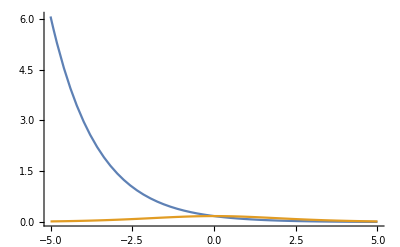

```mathematica
Plot[{Evaluate[Y[t]/.sol],Sech[t/(2 √2)]^2/(4 √2)},{t,-5,5},PlotRange->All]
```

```mathematica
(*Case2*)
```

```mathematica
Quit[];
```

```mathematica
ss=DSolve[{X'[t] == Y[t],
Y'[t]==-(√2/2 )*Y[t]+X[t],X[0]==1/2,Y[0]==1/(4 (√2))},{X[t],Y[t]},{t,-5,5}]
```

{{X[t]→1/12 ⅇ^(-√2 t) (1+5 ⅇ^((3 t)/(√2))),Y[t]→(ⅇ^(-√2 t) (-2+5 ⅇ^((3 t)/(√2))))/(12 √2)}}

```mathematica
sol=Simplify[ExpToTrig[ss]]
```

{{X[t]→1/12 (1+5 Cosh[(3 t)/(√2)]+5 Sinh[(3 t)/(√2)]) (Cosh[√2 t]-Sinh[√2 t]),Y[t]→((-2+5 Cosh[(3 t)/(√2)]+5 Sinh[(3 t)/(√2)]) (Cosh[√2 t]-Sinh[√2 t]))/(12 √2)}}

```mathematica
Plot[{Evaluate[X[t]/.sol],(1/2)*(1+Tanh[(√2*t)/4])},{t,-5,5},PlotRange->All,PlotStyle->{{Red,Dashed,Thick},{Green,DotDashed,Thick}},PlotLabels->{"(ū)_1","u"},Frame->True]
```

-Graphics-

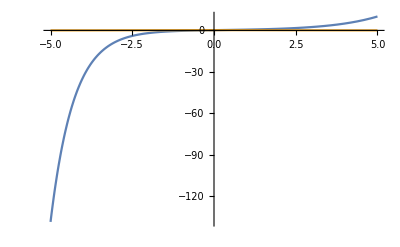

```mathematica
Plot[{Evaluate[Y[t]/.sol],Sech[t/(2 √2)]^2/(4 √2)},{t,-5,5},PlotRange->All]
```

```mathematica
(*Case3*)
```

```mathematica
Quit[];
```

```mathematica
ss=DSolve[{X'[t] == Y[t],
Y'[t]==X[t],X[0]==1/2,Y[0]==1/(4 (√2))},{X[t],Y[t]},{t,-5,5}]
```

{{X[t]→1/16 ⅇ^-t (4-√2+(4+√2) ⅇ^(2 t)),Y[t]→1/16 ⅇ^-t (-4+√2+(4+√2) ⅇ^(2 t))}}

```mathematica
sol=Simplify[ExpToTrig[ss]]
```

{{X[t]→1/8 (4 Cosh[t]+√2 Sinh[t]),Y[t]→1/8 (√2 Cosh[t]+4 Sinh[t])}}

```mathematica
Plot[{Evaluate[X[t]/.sol],(1/2)*(1+Tanh[(√2*t)/4])},{t,-5,5},PlotRange->All,PlotStyle->{{Red,Dashed,Thick},{Green,DotDashed,Thick}},PlotLabels->{"(ū)_1","u"},Frame->True]
```

-Graphics-

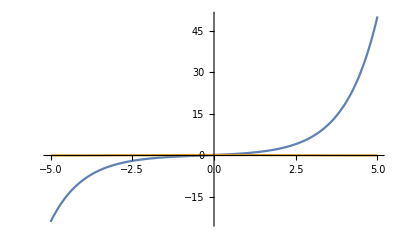

```mathematica
Plot[{Evaluate[Y[t]/.sol],Sech[t/(2 √2)]^2/(4 √2)},{t,-5,5},PlotRange->All]
```